## Initialize

### Set directory, and run axillary files, import .FASTA

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
NotebookEvaluate[AbsoluteFileName["PlotFunctions.nb"]];
NotebookEvaluate[AbsoluteFileName["GeneticFunctions.nb"]];
CurrentValue[$FrontEnd,"NotebookAutoSave"]=True;
```

```mathematica
{EnvelopeAminoSequence}=Characters[Import["env_aa.fasta"]];
HxbNucleotides=Module[{hxbnt,insertions,fullsequence},
hxbnt=Characters[Import["aligned_ref_patient1.fasta"][[1]]];
DeleteCases[hxbnt,"-"]];
```

```mathematica
SequenceOverlap[seq1_,seq2_]:=Total[MapThread[Boole[#1==#2]&,{seq1,seq2}]]
{envZeroPosition}=Ordering[Table[SequenceOverlap[EnvelopeAminoSequence[[1 ;; 20]], (Partition[Drop[HxbNucleotides, ii][[1 ;; 60]], 3] /. codonRules)[[1 ;; 20]]], {ii, 1, Length[HxbNucleotides] - 60}], -1];
```

### Construct coordinate system

```mathematica
SetAttributes[EnvProteinCoordinates,Listable]
EnvProteinCoordinates[envprotein_]:=Range[envZeroPosition+3*envprotein-2,envZeroPosition+3*envprotein]
(*Takes a protein index and returns the three codon locations in HXB.*)
```

```mathematica
RefSeqCoordinates[patient_]:=RefSeqCoordinates[patient]=Block[{hxbnt,alignment,refseqnt,hxbind,refseqind,rules,refseqloc},
(*Generates a function which takes an hxb nt and returns the index of the nt in the reference sequence.*)
alignment=Characters/@Import[StringJoin["aligned_ref_patient",ToString[patient],".fasta"]];
hxbnt=alignment[[1]];
refseqnt=alignment[[2]];
hxbind=Transpose[DeleteCases[Transpose[{hxbnt,Range[Length[hxbnt]]}],{"-",__}]][[2]];
refseqind=Transpose[DeleteCases[Transpose[{refseqnt,Range[Length[hxbnt]]}],{"-",__}]][[2]];
rules=MapThread[Rule,{refseqind,Range[Length[refseqind]]}];
refseqloc=ReplacePart[refseqnt,rules];
With[{a=refseqloc,b=hxbind},Function[hbn,a[[b[[hbn]]]],Listable]]
]
```

```mathematica
RefSeq[patient_]:=RefSeq[patient]=Block[{hxbnt,alignment,refseqnt,hxbind,refseqind,rules,refseqloc},
(*Generates a function which takes an hxb nt and returns the index of the nt in the reference sequence.*)
alignment=Characters/@Import[StringJoin["aligned_ref_patient",ToString[patient],".fasta"]];
hxbnt=alignment[[1]];
refseqnt=alignment[[2]];
hxbind=Transpose[DeleteCases[Transpose[{hxbnt,Range[Length[hxbnt]]}],{"-",__}]][[2]];
With[{a=refseqnt,b=hxbind},Function[hbn,a[[b[[hbn]]]],Listable]]
]
```

### Extract SNPs

```mathematica
PatientDays[patient_]:=PatientDays[patient]=Block[{namelist,days},
(*Returns the days for which we have snp counts*)
SetDirectory[StringJoin["act_p",ToString[patient]]];
namelist=FileNames[RegularExpression[".*tsv"]];
ResetDirectory[];
Sort[ToExpression/@Transpose[StringSplit[#,"_"]&/@namelist][[1]]]]
```

```mathematica
PatientDaySNP[patient_,day_]:=PatientDaySNP[patient,day]=Block[{snpmatrix},
SetDirectory[StringJoin["act_p",ToString[patient]]];
snpmatrix=Drop[Import[StringJoin[ToString[day],"_days.tsv"]],2];
ResetDirectory[];
snpmatrix=Transpose[Drop[Transpose[snpmatrix],-1]];(*drop ambiguious reads*)
With[{mat=snpmatrix},Function[hxbnt,
Block[{coords},coords=RefSeqCoordinates[patient][hxbnt];
If[coords=="-",{0,0,0,0,1},
If[Total[mat[[coords]]]==0,{0,0,0,0,1},
Round[120*mat[[coords]]/Total[mat[[coords]]]]
]
]]
,Listable]]
]
```

```mathematica
PatientDaySNPMat[patient_,day_,amine_]:=PatientDaySNP[patient,day][EnvProteinCoordinates[amine]]
```

```mathematica
SNPCodonFrequency[snpmatrix_,codon_]:=
(*Takes a length-3 list of snps and codon. Returns frequency of codon under indepence of mutations assumption.*)
Block[{ind,normsnp},
ind=codon/.ntRules;
normsnp=Table[N[(snp/Max[Total[snp],1])],{snp,snpmatrix}];
Times@@Table[normsnp[[ii,ind[[ii]] ]],{ii,1,3}]]
```

```mathematica
SNPAArule[patient_,day_,amine_]:=
(*really useful function. Returns a list of rules from amino acids to frequency values*)
Table[aminoAcid->Total[SNPCodonFrequency[PatientDaySNPMat[patient,day,amine],#]&/@(aminoAcid/.aaCodon)]
,{aminoAcid,AAs}];
SNPAAfreq[patient_,day_,amine_]:=
(*Same as above except in vector form*)Table[Total[SNPCodonFrequency[PatientDaySNPMat[patient,day,amine],#]&/@(aminoAcid/.aaCodon)]
,{aminoAcid,AAs}];
```

```mathematica
TemplateCounts[patient_,day_,amine_][{wt_,mut_}]:=
Round[120*Total/@({wt,mut}/.SNPAArule[patient,day,amine])]
```

```mathematica
AAspresent[site_]:=Part[AAs,#]&/@Flatten@Position[Mean[Mean/@Table[SNPAAfreq[pat,day,site],{pat,11},{day,PatientDays[pat]}]],x_/;x>0]
```

## Generate EscSignitures from Bloom data

```mathematica
ablist ={"101074","PGT121","VRC01","VRC34","PG9","PGT151","PGT145","10E8"};
```

```mathematica
mutvec[name_]:=Module[{out},SetDirectory["BloomAntibodies"];out=Drop[Import[#],{1}]&@@FileNames[RegularExpression[".*"<>name<>".*meanmut.*"]]; 
SetDirectory[NotebookDirectory[]];
Return[out]]
sitevec[name_]:=Module[{out},SetDirectory["BloomAntibodies"];out=Drop[Import[#],{1}]&@@FileNames[RegularExpression[".*"<>name<>".*meansite.*"]]; 
SetDirectory[NotebookDirectory[]];
Return[out]]
```

```mathematica
GetMutlist[name_]:= GetMutlist[name]=Module[{mvec,svec,mutlist},
mvec=mutvec[name];
svec=sitevec[name];
mutlist=Table[({#[[1,1]],
DeleteDuplicates[#[[;;,2]]],
DeleteDuplicates[#[[;;,3]]]
})&@Cases[mvec,{ii,a_,b_,c_/;Log[c]>-4}],{ii,svec[[;;5,1]]}];
Return[mutlist]
]
```

```mathematica
GenerateMutationSigniture[site_,muts_]:=Module[{present,wtout,mutout},
present=AAspresent[site];
mutout=Intersection[muts,present];
wtout=DeleteCases[Complement[present,muts],"*"];
If[Length[mutout]>0,
Return[{site,wtout,mutout}],
Return[Nothing]]
]
```

```mathematica
escaperules=Table[ab->(GenerateMutationSigniture[#[[1]],#[[3]]]&/@GetMutlist[ab]),{ab,ablist}]
```

{101074→{{325,{D,N},{E,G,K,S}},{334,{S},{D,G,N}},{332,{N},{A,D,E,I,K,T,V}},{330,{F,H,L,Q,S,Y},{R}}},PGT121→{{334,{D,S},{G,N}},{332,{A,E,N,V},{D,I,K,T}},{330,{F,H,L,R,S,Y},{Q}}},VRC01→{{197,{D,N},{S}}},VRC34→{{88,{N},{K}},{90,{S,T},{A,E,K}},{85,{G,H},{A,C,D,E,F,I,K,L,N,P,Q,R,S,T,V,Y}},{524,{G,P},{A,E,R,S}},{512,{A},{G,T}}},PG9→{{160,{N},{K,Y}},{171,{K,P,R},{A,E,G,H,N,Q,S,T}},{169,{G,I,K,M,R,V,W},{E,L,T}},{162,{S,T},{A,I,P}}},PGT151→{{613,{S,T},{C,N}},{611,{G,N},{D,S}},{512,{A},{G,T}},{637,{D,N},{E,K,S,T}},{639,{T},{I,M}}},PGT145→{{166,{K,R},{A,E,G,S,T}},{160,{N},{K,Y}},{169,{G,I,K,L,T,V},{E,M,R,W}},{121,{K},{E}},{162,{S,T},{A,I,P}}},10E8→{{671,{K,N,S},{R,T}},{673,{F},{L,V}}}}

```mathematica
escaperules = escaperules /. "VRC01" -> "VRC01_dms";
```

```mathematica
(*These were called using the clinical trial data and the occurance of mutations. Bloom data was very noisy for 3BNC, and so not used*)
```

```mathematica
altEscapeRules={"10-1074"->{{325,{"D","N"},{"E","G","K"}},{332,{"N"},{"D","H","I","K","S","T","Y"}},{334,{"S"},{"A","F","G","I","N","R","Y"}}},"3BNC117"->{{279,{"D","N"},{"A","H","K"}},{281,{"A","P"},{"T","V"}},{282,{"K","Y"},{"E","N","R"}},{459,{"G"},{"D","N"}}},
"VRC01"->{{197,{"D","N"},{"S"}},{279,{"D","N"},{"A","H","K"}},{280,{"N"},{"D"}},{281,{"A","P"},{"T","V"}},{458,{"G"},{"D"}}}
};
```

```mathematica
EscSignitures=Join[escaperules,altEscapeRules];
```

## Analyze population size and transition/transversion ratio

```mathematica
SNPFullSum[amine_]:=SNPFullSum[amine]=Plus@@Table[Plus@@Table[PatientDaySNPMat[patient,day,amine],{day,PatientDays[patient]}],{patient,1,11}]
(*Returns the sum over all snp matrices*)
```

```mathematica
ConservedAmino[amine_]:=Total[Table[(aminoAcid/.binaryAminos)*Total[SNPCodonFrequency[SNPFullSum[amine],#]&/@(aminoAcid/.aaCodon)]^2
,{aminoAcid,AAs}]]
```

```mathematica
conservedBinaryInd=First/@Select[Table[{ii,ConservedAmino[ii]},{ii,Length[EnvelopeAminoSequence]}],(Part[#,2]>.96)&];
```

```mathematica
FourfoldConservedAmino[amine_]:=Total[Table[(aminoAcid/.fourfoldAminos)*Total[SNPCodonFrequency[SNPFullSum[amine],#]&/@(aminoAcid/.aaCodon)]^2
,{aminoAcid,AAs}]]
```

```mathematica
conservedFourfoldInd=First/@Select[Table[{ii,FourfoldConservedAmino[ii]},{ii,Length[EnvelopeAminoSequence]}],(Part[#,2]>.96)&];
```

```mathematica
BernoulliCounts[patient_,day_,amino_]:=Part[PatientDaySNP[patient,day][EnvProteinCoordinates[amino][[3]]](*Look at the third position in the codon*),(Part[#,3]&/@(AAs[[Sequence@@Ordering[SNPAAfreq[patient,day,amino],-1]
(*Look at the most common amino acid, find it's name and it's codon, take the codon letters in the third postion and convert to indices in ntRules*)]]/.aaCodon))/.ntRules]
```

```mathematica
PurinePyrimidineCounts[patient_,day_,amino_]:=Table[Total[Part[PatientDaySNP[patient,day][EnvProteinCoordinates[amino][[3]]],p/.ntRules]],{p,{{"A","G"},{"C","T"}}}]
```

```mathematica
Neutralθts[patient_,day_]:=Neutralθts[patient,day]=
FindNeutralθ[Table[BernoulliCounts[patient,day,ii],{ii,conservedBinaryInd}]]
```

```mathematica
Neutralθtv[patient_,day_]:=Neutralθtv[patient,day]=
1/2 FindNeutralθ[Table[PurinePyrimidineCounts[patient,day,ii],{ii,conservedFourfoldInd}]]
```

```mathematica
transversionRatio=(#[[1]])/(#[[2]])&@(Eigenvectors[Total@Table[{x}ᵀ.{x},{x,Join@@Table[Table[{Neutralθts[patient,day],Neutralθtv[patient,day]},{day,PatientDays[patient]}],{patient,11}]}]][[1]])
```

7.57586

```mathematica
θts[patient_,day_]:={Neutralθts[patient,day],Neutralθtv[patient,day]}.Normalize[{transversionRatio,1}]*Normalize[{transversionRatio,1}][[1]]
```

## SFS plots

```mathematica
ImExport["sfs_allpatients",Show[Plot[{},{x,-.5,0},PlotRange->{{-2.2,-.2},{0,3}},FrameTicks->{{LogTicks[0,3],LogTicks[0,3,ShowTickLabels->False]},{LogTicks[-3,0],LogTicks[-3,0,ShowTickLabels->False]}},
AspectRatio->1,
PlotLegends->Placed[LineLegend[{RGBColor[0.47000000000000003, 0.64, 0.74]},{"Neutral theory\n (constant θ)"}],{.7,.7}],
FrameLabel->{"Frequency (X)","Obeservations"}
],Graphics[{RGBColor[0.47000000000000003, 0.64, 0.74],AbsoluteThickness[2],
Line@Table[{Log10[x/120],Log10[320000*PDF[BetaBinomialDistribution[.001,.001,120],x]]},{x,1,60}],Black,pts
}

]],{1,1}]
```

Figures/sfs_allpatients.pdf

```mathematica
pts = Point[List@@#]&/@Normal[Log10[Drop[Counts[Log10[1-Join@@Table[Join@@Table[Function[x,If[And[θts[pat,day]>0.0001,Total[x]==120],Max[x]/Total[x],Nothing]]/@(
Join[PurinePyrimidineCounts[pat,day,#]&/@conservedFourfoldInd,
BernoulliCounts[pat,day,#]&/@conservedBinaryInd]
),{day,PatientDays[pat]}],{pat,11}]]],{1}]]];
```

```mathematica
Point[List@@#]&/@Normal[Log10[Drop[Counts[Log10[1-Join@@Table[Join@@Table[Function[x,If[And[θts[pat,day]>0.0001,Total[x]==120],Max[x]/Total[x],Nothing]]/@(
Join[PurinePyrimidineCounts[pat,day,#]&/@conservedFourfoldInd,
BernoulliCounts[pat,day,#]&/@conservedBinaryInd]
),{day,PatientDays[pat]}],{pat,11}]]],{1}]]]
```

```mathematica
patients=ToString/@Range[11]
```

{1,2,3,4,5,6,7,8,9,10,11}

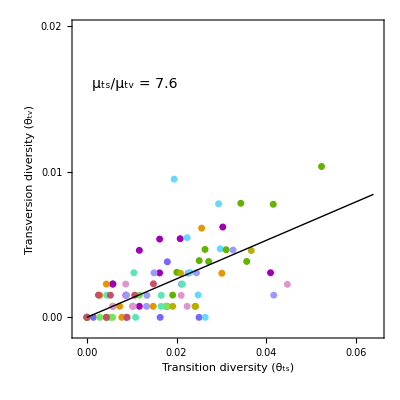

```mathematica
PlotPopSize[Table[Table[Neutralθts[patient,day],{day,PatientDays[patient]}],{patient,1,11}],Table[Table[Neutralθtv[patient,day],{day,PatientDays[patient]}],{patient,1,11}]]
```

```mathematica
ImExport["snp_popsize",PlotPopSize[Table[Table[Neutralθts[patient,day],{day,PatientDays[patient]}],{patient,1,11}],Table[Table[Neutralθtv[patient,day],{day,PatientDays[patient]}],{patient,1,11}]],{1,1}]
```

Figures/snp_popsize.pdf

## Mutation rates and counts

```mathematica
EscRates=Map[Rule[#[[1]],μνRates[transversionRatio][#[[2]],#[[3]]]]&,EscSignitures,{3}];
```

```mathematica
abnames=First/@EscSignitures
```

{101074,PGT121,VRC01_dms,VRC34,PG9,PGT151,PGT145,10E8,10-1074,3BNC117,VRC01}

## Export to HDF5

One of the tricky things is that HDF5 exporter seems to be unstable in the ordering of data for analysis. We’ve had to tightly bind the

```mathematica
cladeb=DeleteCases[6]@DeleteCases[1]@Range[11]
```

{2,3,4,5,7,8,9,10,11}

```mathematica
vals=Association@Table[ab->Association@@Table["site"<>ToString[site[[1]]]->
Association[
"loc"->site[[1]],
"wt_mut_aa"->site[[{2,3}]],
"mut"->site[[1]]/.(ab/.EscRates),
"snpdata"->
Association@Table[{"patient"<>ToString[p]->
Association@Table["day"<>ToString[d]->
Association[
"theta"->θts[p,d],
"kwt_mut"->TemplateCounts[p,d,site[[1]] ][site[[{2,3}]]]
]
,{d,PatientDays[p]}]
},{p,cladeb}]
],{site,(ab/.EscSignitures)}],{ab,abnames}];
```

## Export

```mathematica
ExportStructuredHDF5["snpanalysis_cladeb.h5",vals]
```

## Coat Plots

```mathematica
PowerRefit[p_][vec_]:=vec^p/Total[vec^p]
```

```mathematica
StackedFreqPlot[patient_,pt_]:=
Block[{vals,ns},
vals=Transpose@Table[
If[Total[Flatten@PatientDaySNPMat[patient,day,pt]]>4,
{day,#}&/@PowerRefit[.3][Chop[SNPAAfreq[patient,day,pt],1*10^-3]],Nothing],{day,PatientDays[patient]}];
StackedListPlot[vals,
InterpolationOrder->1,Axes->False,AspectRatio->1/8,ImagePadding->None,PlotRangeClipping->False,PlotRangePadding->None,FrameStyle->AbsoluteThickness[.5],
Frame->True,FrameTicks->None,
PlotStyle->(Directive[AbsoluteThickness[.1],#]&/@(AAs/.aminoColorScheme)),FillingStyle->Opacity[1]]];
```

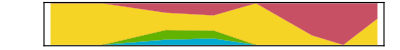

```mathematica
StackedFreqPlot[4,325]
```

```mathematica
opts={FontFamily->"Arial",FontSize->14,FontColor->Black};
```

```mathematica
EscapePlot[patient_,escapesites_]:=Block[{xticks,yticks,pt,days},
yticks=Table[{ii,ToString/@escapesites[[ii]]},{ii,Length[escapesites]}];
pt=First[escapesites];
days=Table[
If[Total[Flatten@PatientDaySNPMat[patient,day,pt]]>4,
day,Nothing],{day,PatientDays[patient]}];
xticks=Table[{ii,DecimalForm[(Min[days]+(4.+ii)/8 Through[{Min,Max}[days]].{-1,1})/365.,{2,1}]},{ii,-3,3,2}];
Graphics[Table[Inset[StackedFreqPlot[patient,escapesites[[ii]]],{0,ii},Center,{8,1.0}],{ii,Length[escapesites]}],PlotRange->{{-4,4},{.5,Length[escapesites]+.5}},Frame->True,FrameTicks->{{yticks,None},{xticks,None}},PlotRangePadding->None,
FrameLabel->{{None,Rotate[Text[StringJoin["Patient ",ToString[patient]]],π]},{None,None}}
,LabelStyle->Evaluate@opts,
FrameStyle->AbsoluteThickness[1.0],TicksStyle->AbsoluteThickness[1.0]]
]
```

```mathematica
Table[ImExport["escp_muller10-1074-"<>ToString[pat],EscapePlot[pat,{325,332,334}],{1,3/8}],{pat,1,11}]
```

{Figures/escp_muller10-1074-1.pdf,Figures/escp_muller10-1074-2.pdf,Figures/escp_muller10-1074-3.pdf,Figures/escp_muller10-1074-4.pdf,Figures/escp_muller10-1074-5.pdf,Figures/escp_muller10-1074-6.pdf,Figures/escp_muller10-1074-7.pdf,Figures/escp_muller10-1074-8.pdf,Figures/escp_muller10-1074-9.pdf,Figures/escp_muller10-1074-10.pdf,Figures/escp_muller10-1074-11.pdf}

```mathematica
aminoColorScheme
```

<|A→RGBColor[0.7294117647058823, 0.7529411764705882, 0.9764705882352941],C→RGBColor[0.047058823529411764, 0.8509803921568627, 0.9921568627450981],D→RGBColor[0.9372549019607843, 0.26666666666666666, 0.30196078431372547],E→RGBColor[0.792156862745098, 0.4235294117647059, 0.5019607843137255],F→RGBColor[0.22745098039215686, 0.5764705882352941, 0.44313725490196076],G→RGBColor[0.8, 0.4117647058823529, 0.],H→RGBColor[1., 0.6980392156862745, 0.03529411764705882],I→RGBColor[0.09411764705882353, 0.5372549019607843, 0.8274509803921568],K→RGBColor[1., 0.6862745098039216, 0.6862745098039216],L→RGBColor[0.20784313725490197, 0.6235294117647059, 0.9254901960784314],M→RGBColor[0.37254901960784315, 0.5215686274509804, 0.7450980392156863],N→RGBColor[0.996078431372549, 0.3215686274509804, 0.03137254901960784],P→RGBColor[0.9176470588235294, 0.09803921568627451, 0.8352941176470589],Q→RGBColor[0.9607843137254902, 0.7058823529411765, 0.803921568627451],R→RGBColor[0.996078431372549, 0.7098039215686275, 0.6352941176470588],S→RGBColor[0.5764705882352941, 0.49411764705882355, 0.5529411764705883],T→RGBColor[0.8549019607843137, 0.7137254901960784, 0.9725490196078431],V→Hue[0.5285714285714286, 1, 0.81],W→RGBColor[0.4470588235294118, 0.8745098039215686, 0.24705882352941178],Y→RGBColor[0.4196078431372549, 0.5529411764705883, 0.3686274509803922],*→GrayLevel[0.32]|>